```mathematica
(* Subscript[I, 2](l,L)-Subscript[I, 2](L/2,L)
=c/2 ln[(f(l/L) f((L-l)/L))/(f(1/2))^2]
where f(x)=Dedekindeta(ix) *)
```

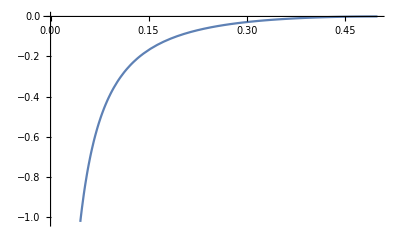

```mathematica
Clear[J,l,L,x,F];
(* for ising model *)
c=0.5;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
Plot[c/2 Log[F[x]],{x,0,0.5}]
```

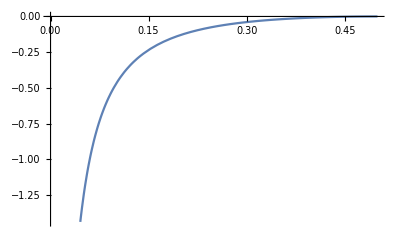

```mathematica
Clear[J,l,L,x,F,c];
(* for classical Blume-Capel model *)
c=7/10;
F[x_]:=(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2;
p=Plot[c/2 Log[F[x]],{x,0,0.5}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]]
a=Flatten[Import["x-data.dat"]];
b=Flatten[Import["y-data.dat"]];
data=Transpose[{a,b}];
l=ListPlot[data];
(*******************)
Clear[J,x,F,c];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pfit=Plot[J[0.45660428321298474,x],{x,0,0.5}];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pfit,l,PlotRange->{-0.2,0}]
Show[pactual,l,PlotRange->{-0.2,0}]*)
```

```mathematica
(* fit data *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import["SCANDATA.dat"];
a=d[[;;,3]];
b=d[[;;,7]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&]
l=ListPlot[data];
```

{{0.11111,-0.18098},{0.125,-0.13044},{0.125,-0.16505},{0.14286,-0.15634},{0.15,-0.10402},{0.16667,-0.08996},{0.16667,-0.15228},{0.1875,-0.08245},{0.2,-0.06217},{0.2,-0.13192},{0.20833,-0.06852},{0.21429,-0.07368},{0.22222,-0.05281},{0.25,-0.04183},{0.25,-0.1129},{0.25,-0.06303},{0.25,-0.04732},{0.27778,-0.02897},{0.28571,-0.03327},{0.29167,-0.03143},{0.3,-0.04186},{0.3125,-0.02132},{0.33333,-0.01723},{0.33333,-0.02792},{0.35,-0.0104},{0.35714,-0.01502},{0.375,-0.02367},{0.375,-0.01126},{0.38889,-0.00639},{0.4,-0.00378},{0.4,-0.00544},{0.41667,-0.00802},{0.42857,-0.00533},{0.4375,-0.00451},{0.44444,0.00235},{0.45,-0.0008},{0.45833,-0.00762},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.}}

{c→0.51552}

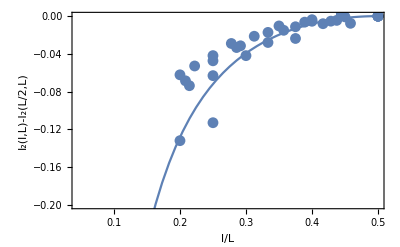

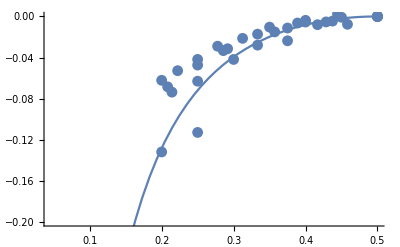

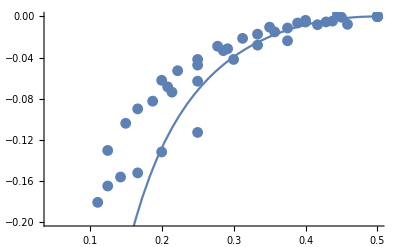

```mathematica
datanew={{0.2,-0.06217},{0.2,-0.13192},{0.20833,-0.06852},{0.21429,-0.07368},{0.22222,-0.05281},{0.25,-0.04183},{0.25,-0.1129},{0.25,-0.06303},{0.25,-0.04732},{0.27778,-0.02897},{0.28571,-0.03327},{0.29167,-0.03143},{0.3,-0.04186},{0.3125,-0.02132},{0.33333,-0.01723},{0.33333,-0.02792},{0.35,-0.0104},{0.35714,-0.01502},{0.375,-0.02367},{0.375,-0.01126},{0.38889,-0.00639},{0.4,-0.00378},{0.4,-0.00544},{0.41667,-0.00802},{0.42857,-0.00533},{0.4375,-0.00451},{0.44444,0.00235},{0.45,-0.0008},{0.45833,-0.00762},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.}};
lnew=ListPlot[datanew];
fit=FindFit[datanew,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pfit=Plot[J[0.7,x],{x,0,0.5}];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pfit,lnew,PlotRange->{-0.2,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"}]
Show[pactual,lnew,PlotRange->{-0.2,0}]
Show[pactual,l,PlotRange->{-0.2,0}]
```

L=8

{c→1.2663}

L=10

{c→0.721484}

L=12

{c→0.569695}

L=14

{c→0.435541}

L=16

{c→0.364474}

L=18

{c→0.323845}

L=20

{c→0.323452}

L=24

{c→0.297631}

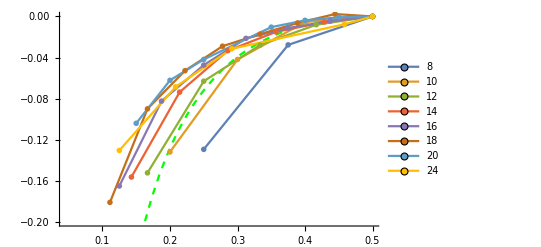

all-data-ips.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
marker1=Graphics[{Disk[]}];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
(*******************)
d8=Import["SCANDATA-8.dat"];
a8=d8[[;;,3]];
b8=d8[[;;,7]];
(*data8=Transpose[{a8,b8}];*)
data8=Sort[Transpose[{a8,b8}],#1[[1]]<#2[[1]]&];
l8=ListLinePlot[data8,PlotStyle->Cyan,PlotMarkers->{marker1,.03}];
"L=8"
fit8=FindFit[data8,J[c,x],{c},x]
(*******************)
d10=Import["SCANDATA-10.dat"];
a10=d10[[;;,3]];
b10=d10[[;;,7]];
(*data10=Transpose[{a10,b10}];*)
data10=Sort[Transpose[{a10,b10}],#1[[1]]<#2[[1]]&];
l10=ListLinePlot[data10,PlotStyle->Black,PlotMarkers->{marker1,.03}];
"L=10"
fit10=FindFit[data10,J[c,x],{c},x]
(*******************)
d12=Import["SCANDATA-12.dat"];
a12=d12[[;;,3]];
b12=d12[[;;,7]];
(*data12=Transpose[{a12,b12}];*)
data12=Sort[Transpose[{a12,b12}],#1[[1]]<#2[[1]]&];
l12=ListLinePlot[data12,PlotStyle->Gray,PlotMarkers->{marker1,.03}];
"L=12"
fit12=FindFit[data12,J[c,x],{c},x]
(*******************)
d14=Import["SCANDATA-14.dat"];
a14=d14[[;;,3]];
b14=d14[[;;,7]];
(*data14=Transpose[{a14,b14}];*)
data14=Sort[Transpose[{a14,b14}],#1[[1]]<#2[[1]]&];
l14=ListLinePlot[data14,PlotStyle->Blue,PlotMarkers->{marker1,.03}];
"L=14"
fit14=FindFit[data14,J[c,x],{c},x]
(*******************)
d16=Import["SCANDATA-16.dat"];
a16=d16[[;;,3]];
b16=d16[[;;,7]];
(*data16=Transpose[{a16,b16}];*)
data16=Sort[Transpose[{a16,b16}],#1[[1]]<#2[[1]]&];
l16=ListLinePlot[data16,PlotStyle->Green,PlotMarkers->{marker1,.03}];
"L=16"
fit16=FindFit[data16,J[c,x],{c},x]
(****************************)
d18=Import["SCANDATA-18.dat"];
a18=d18[[;;,3]];
b18=d18[[;;,7]];
(*data18=Transpose[{a18,b18}];*)
data18=Sort[Transpose[{a18,b18}],#1[[1]]<#2[[1]]&];
l18=ListLinePlot[data18,PlotStyle->Orange,PlotMarkers->{marker1,.03}];
"L=18"
fit18=FindFit[data18,J[c,x],{c},x]
(****************************)
d20=Import["SCANDATA-20.dat"];
a20=d20[[;;,3]];
b20=d20[[;;,7]];
(*data20=Transpose[{a20,b20}];*)
data20=Sort[Transpose[{a20,b20}],#1[[1]]<#2[[1]]&];
l20=ListLinePlot[data20,PlotStyle->Yellow,PlotMarkers->{marker1,.03}];
"L=20"
fit20=FindFit[data20,J[c,x],{c},x]
(****************************)
d24=Import["SCANDATA-24.dat"];
a24=d24[[;;,3]];
b24=d24[[;;,7]];
data24=Sort[Transpose[{a24,b24}],#1[[1]]<#2[[1]]&];
l24=ListLinePlot[data24,PlotStyle->Red,PlotMarkers->{marker1,.03}];
"L=24"
fit24=FindFit[data24,J[c,x],{c},x]
(***********************************)
Clear[J,x,F,c,pfit,pactual,LLL];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5},PlotStyle->{Green,Dashed}];
LLL=ListLinePlot[{data8,data10,data12,data14,data16,data18,data20,data24},PlotLegends->{8,10,12,14,16,18,20,24},PlotMarkers->{marker1,.03}];
s=Show[pactual,LLL,PlotRange->{-0.2,0}]
Export["all-data-ips.pdf",s]
(*Show[pactual,l8,l10,l12,l14,l12,l16,l18,l20,l24,PlotRange->{-0.2,0}]*)
```

```mathematica
Sort[data12,#1[[1]]<#2[[1]]&]
Sort[data16,#1[[1]]<#2[[1]]&]
Sort[data18,#1[[1]]<#2[[1]]&]
Sort[data24,#1[[1]]<#2[[1]]&]
```

{{0.16667,-0.15228},{0.25,-0.06303},{0.33333,-0.02792},{0.41667,-0.00802},{0.5,0.}}

{{0.125,-0.16505},{0.1875,-0.08245},{0.25,-0.04732},{0.3125,-0.02132},{0.375,-0.01126},{0.4375,-0.00451},{0.5,0.}}

{{0.11111,-0.18098},{0.16667,-0.08996},{0.22222,-0.05281},{0.27778,-0.02897},{0.33333,-0.01723},{0.38889,-0.00639},{0.44444,0.00235},{0.5,0.}}

{{0.125,-0.13044},{0.20833,-0.06852},{0.29167,-0.03143},{0.45833,-0.00762},{0.5,0.}}

```mathematica
J[0.7,0.125]
J[0.7,0.16667]
```

-0.326834

-0.190529

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import["SCANDATA.dat"];
(*d=Import["s.dat"];*)
a=d[[;;,3]];
b=d[[;;,7]];
data=Transpose[{a,b}];
Sort[data,#1[[1]]<#2[[1]]&]
l=ListPlot[data];
```

{{0.11111,-0.16979},{0.125,-0.13043},{0.125,-0.16325},{0.14286,-0.15224},{0.15,-0.09738},{0.16667,-0.08186},{0.16667,-0.14829},{0.16667,-0.09333},{0.1875,-0.08124},{0.2,-0.05386},{0.2,-0.12766},{0.20833,-0.07136},{0.21429,-0.07127},{0.22222,-0.04889},{0.25,-0.03707},{0.25,-0.10613},{0.25,-0.06017},{0.25,-0.04578},{0.25,-0.04648},{0.27778,-0.02306},{0.28571,-0.03475},{0.29167,-0.03645},{0.3,-0.04289},{0.3125,-0.02392},{0.33333,-0.0122},{0.33333,-0.02575},{0.33333,-0.02191},{0.35,-0.00372},{0.35714,-0.01745},{0.375,-0.02059},{0.375,-0.01184},{0.38889,-0.00471},{0.4,-0.00066},{0.4,-0.00616},{0.41667,-0.00813},{0.42857,-0.00735},{0.4375,-0.00529},{0.44444,0.0049},{0.45,0.00362},{0.45833,-0.00653},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.},{0.5,0.}}

{c→0.491274}

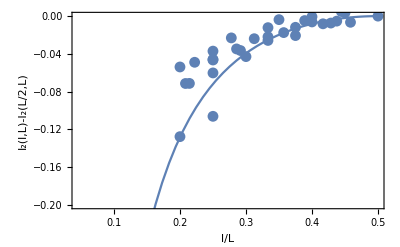

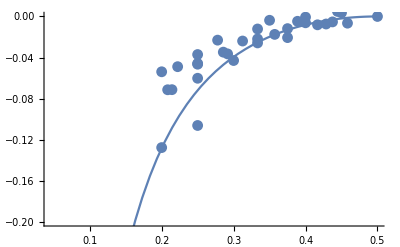

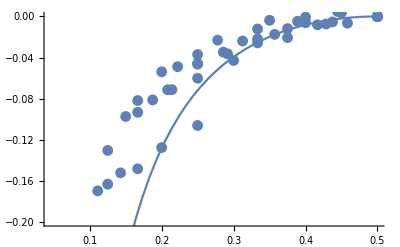

```mathematica
datanew={{0.2,-0.05386},{0.2,-0.12766},{0.20833,-0.07136},{0.21429,-0.07127},{0.22222,-0.04889},{0.25,-0.03707},{0.25,-0.10613},{0.25,-0.06017},{0.25,-0.04578},{0.25,-0.04648},{0.27778,-0.02306},{0.28571,-0.03475},{0.29167,-0.03645},{0.3,-0.04289},{0.3125,-0.02392},{0.33333,-0.0122},{0.33333,-0.02575},{0.33333,-0.02191},{0.35,-0.00372},{0.35714,-0.01745},{0.375,-0.02059},{0.375,-0.01184},{0.38889,-0.00471},{0.4,-0.00066},{0.4,-0.00616},{0.41667,-0.00813},{0.42857,-0.00735},{0.4375,-0.00529},{0.44444,0.0049},{0.45,0.00362},{0.45833,-0.00653},{0.5,0.}};
lnew=ListPlot[datanew];
fit=FindFit[datanew,J[c,x],{c},x]
(*******************)
Clear[J,x,F,c,pfit,pactual];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pfit=Plot[J[0.7,x],{x,0,0.5}];
pactual=Plot[J[0.7,x],{x,0,0.5}];
Show[pfit,lnew,PlotRange->{-0.2,0},Frame->True,FrameLabel->{"l/L","I_2(l,L)-I_2(L/2,L)"}]
Show[pactual,lnew,PlotRange->{-0.2,0}]
Show[pactual,l,PlotRange->{-0.2,0}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
marker1=Graphics[{Disk[]}];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
d24=Import["SCANDATA-24.dat"];
d18=Import["SCANDATA-18.dat"];
d20=Import["SCANDATA-20.dat"];
(*******************)
d8=Import["SCANDATA-8.dat"];
a8=d8[[;;,3]];
b8=d8[[;;,7]];
(*data8=Transpose[{a8,b8}];*)
data8=Sort[Transpose[{a8,b8}],#1[[1]]<#2[[1]]&];
l8=ListPlot[data8,PlotStyle->Cyan,PlotMarkers->{marker1,.03}];
"L=8"
fit8=FindFit[data8,J[c,x],{c},x]
(*******************)
d10=Import["SCANDATA-10.dat"];
a10=d10[[;;,3]];
b10=d10[[;;,7]];
(*data10=Transpose[{a10,b10}];*)
data10=Sort[Transpose[{a10,b10}],#1[[1]]<#2[[1]]&];
l10=ListPlot[data10,PlotStyle->Black,PlotMarkers->{marker1,.03}];
"L=10"
fit10=FindFit[data10,J[c,x],{c},x]
(*******************)
d12=Import["SCANDATA-12.dat"];
a12=d12[[;;,3]];
b12=d12[[;;,7]];
(*data12=Transpose[{a12,b12}];*)
data12=Sort[Transpose[{a12,b12}],#1[[1]]<#2[[1]]&];
l12=ListPlot[data12,PlotStyle->Gray,PlotMarkers->{marker1,.03}];
"L=12"
fit12=FindFit[data12,J[c,x],{c},x]
(*******************)
d14=Import["SCANDATA-14.dat"];
a14=d14[[;;,3]];
b14=d14[[;;,7]];
(*data14=Transpose[{a14,b14}];*)
data14=Sort[Transpose[{a14,b14}],#1[[1]]<#2[[1]]&];
l14=ListPlot[data14,PlotStyle->Blue,PlotMarkers->{marker1,.03}];
"L=14"
fit14=FindFit[data14,J[c,x],{c},x]
(*******************)
d16=Import["SCANDATA-16.dat"];
a16=d16[[;;,3]];
b16=d16[[;;,7]];
(*data16=Transpose[{a16,b16}];*)
data16=Sort[Transpose[{a16,b16}],#1[[1]]<#2[[1]]&];
l16=ListPlot[data16,PlotStyle->Green,PlotMarkers->{marker1,.03}];
"L=16"
fit16=FindFit[data16,J[c,x],{c},x]
(****************************)
a18=d18[[;;,3]];
b18=d18[[;;,7]];
(*data18=Transpose[{a18,b18}];*)
data18=Sort[Transpose[{a18,b18}],#1[[1]]<#2[[1]]&];
l18=ListPlot[data18,PlotStyle->Orange,PlotMarkers->{marker1,.03}];
"L=18"
fit18=FindFit[data18,J[c,x],{c},x]
(****************************)
a20=d20[[;;,3]];
b20=d20[[;;,7]];
(*data20=Transpose[{a20,b20}];*)
data20=Sort[Transpose[{a20,b20}],#1[[1]]<#2[[1]]&];
l20=ListPlot[data20,PlotStyle->Yellow,PlotMarkers->{marker1,.03}];
"L=20"
fit20=FindFit[data20,J[c,x],{c},x]
(****************************)
a24=d24[[;;,3]];
b24=d24[[;;,7]];
data24=Sort[Transpose[{a24,b24}],#1[[1]]<#2[[1]]&];
l24=ListPlot[data24,PlotStyle->Red,PlotMarkers->{marker1,.03}];
"L=24"
fit24=FindFit[data24,J[c,x],{c},x]
(***********************************)
Clear[J,x,F,c,pfit,pactual,LLL];
J[c_,x_]:=c/2 Log[(DedekindEta[ⅈ x]*DedekindEta[ⅈ (1-x)])/DedekindEta[ⅈ /2]^2];
pactual=Plot[J[0.7,x],{x,0,0.5},PlotStyle->{Green,Dashed}];
LLL=ListLinePlot[{data8,data10,data12,data14,data16,data18,data20,data24},PlotLegends->{8,10,12,14,16,18,20,24},PlotMarkers->{marker1,.03}];
Show[pactual,LLL,PlotRange->{-0.2,0}]
```

L=8

{c→1.2663}

L=10

{c→0.721484}

L=12

{c→0.569695}

L=14

{c→0.435541}

L=16

{c→0.364474}

L=18

{c→0.323845}

L=20

{c→0.323452}

L=24

{c→0.297631}

-Graphics-